```mathematica
dataDrive=Flatten[Import["C:\\Users\\apc\\Documents\\Python Scripts\\Cold Control Heavy\\waveforms\\new_Tom\\Sin4 intensity pulse\\614 drive_0 pad\\sin4_100_614.csv"]];
dataDepump=Flatten[Import["C:\\Users\\apc\\Documents\\Python Scripts\\Cold Control Heavy\\waveforms\\new_Tom\\Tophat\\202 long\\160 drive\\tophat_100_202.csv"]];
```

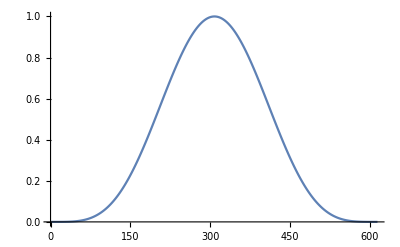
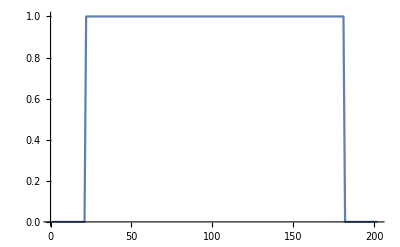

```mathematica
MinMax[data];
{ListLinePlot[dataDrive],ListLinePlot[dataDepump]}
```

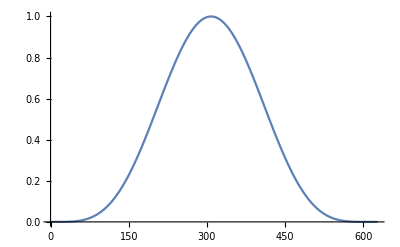
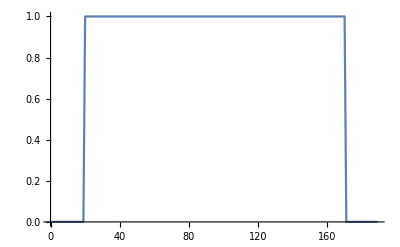

{{627,189},816}

```mathematica
padding=13;
dataNewDrive=PadRight[dataDrive,614+padding,0];
lenTophat=202-padding;
lenPadTophat=Round[lenTophat*0.2,2];
lenDriveTophat=lenTophat-lenPadTophat;
dataNewTophat= PadLeft[PadRight[PadRight[{},lenDriveTophat,1],lenTophat-lenPadTophat/2,0],lenTophat,0];
{ListLinePlot[dataNewDrive],ListLinePlot[dataNewTophat]}
{#,Total[#]}&@(Length/@{dataNewDrive,dataNewTophat})
```

```mathematica
(*subpowers*)
folderDriveName="C:\\Users\\apc\\Documents\\Python Scripts\\Cold Control Heavy\\waveforms\\new_Tom\\Sin4 intensity pulse\\614 drive_"<>ToString@padding<>" prepad"
folderDepumpName="C:\\Users\\apc\\Documents\\Python Scripts\\Cold Control Heavy\\waveforms\\new_Tom\\Tophat\\"<>ToString@lenTophat<>" long\\"<>ToString@lenDriveTophat<>" drive"
If[DirectoryQ[folderDriveName],None,CreateDirectory[folderDriveName]]
If[DirectoryQ[folderDepumpName],None,CreateDirectory[folderDepumpName]]
δ=10^-5;
Table[
Export[folderDriveName<>"\\sin4_"<>ToString[i]<>"_"<>ToString@Length@dataNewDrive<>".csv",N@Chop[{i/100 dataNewDrive},δ]],
{i,5,100,5}
]
Table[
Export[folderDepumpName<>"\\tophat_"<>ToString[i]<>"_"<>ToString@Length@dataNewTophat<>".csv",N@Chop[{i/100 dataNewTophat},δ]],
{i,5,100,5}
]
```

C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad

C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive

C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad

C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive

{C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_5_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_10_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_15_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_20_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_25_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_30_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_35_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_40_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_45_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_50_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_55_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_60_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_65_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_70_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_75_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_80_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_85_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_90_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_95_627.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Sin4 intensity pulse\614 drive_13 prepad\sin4_100_627.csv}

{C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_5_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_10_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_15_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_20_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_25_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_30_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_35_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_40_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_45_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_50_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_55_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_60_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_65_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_70_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_75_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_80_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_85_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_90_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_95_189.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\189 long\151 drive\tophat_100_189.csv}

```mathematica
Table[
Export["C:\\Users\\apc\\Documents\\Python Scripts\\Cold Control Heavy\\waveforms\\new_Tom\\Sin4 intensity pulse\\614 drive_"<>ToString[padding]<>" pad\\sin4_"<>ToString[i]<>"_614.csv",N@Chop[{i/100 dataNew},δ]],
{i,5,95,10}
]
```